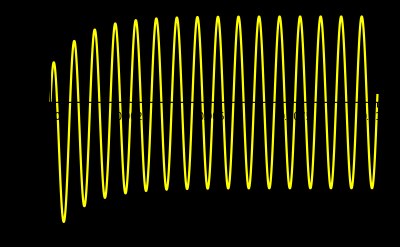

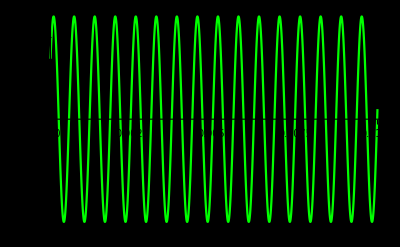

```mathematica
ClearAll["Global*`"];

u[t_] := 5*Sin[10^4*t + 2.1];
R1 = 1*10^3;
C1 = 1*10^-6;
tmax = 0.01;

(* Klasické ND řešení *)

reseni = NDSolve[{
0 == iz[t] + ir[t],
ir[t] == ic[t],

u1[t] - u2[t] == R1 * ir[t],
ic[t] == C1 * u2'[t],
u2[0] == 0,
u[t] == u1[t]
}, {u1[t], u2[t], ir[t], ic[t], iz[t]}, {t, 0, tmax}, StartingStepSize-> 10^-9];

(* Vykreslení grafu - pozor na parametry *)
Plot[u2[t] /. reseni[[1]], {t, 0, tmax}, PlotStyle -> Yellow, PlotLegends -> "u3(t)", Background -> Black, PlotRange -> All]

(* Nyní harmonický stav řešení *)
ω = 10^4;
φ = 2.1;

u = 5*Exp[ⅉ*2.1];
rovnice = {
ir1 == ic1,
u-u21 == R1*ir1,
ic1 == C1 * ⅉ * ω * u21
};

reseniHUS1 = Solve[rovnice];
Plot[{Im[u21 * Exp[ⅉ*ω*t]]/. reseniHUS1}, {t, 0, tmax}, PlotStyle -> Green, Background -> Black, PlotRange -> All]
```

```mathematica
'
```